```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Interpolation

Suppose someone said: “I’m thinking of three numbers. The first number is 10, the third number is 20. What’s the second number?” Of course it’s impossible to know for sure, but a good guess would be the number halfway between the first and the third, in this case 1/2 (10+20) = 15. This is an example of interpolation, of guessing values at some intermediate position from the surrounding values. While many uses of interpolation are two dimensional (for instance, almost all spatial mappings require interpolation), it is best to start simple.  In order to see how interpolation works, consider the one-dimensional case.

```mathematica
TableForm[{{Hyperlink["InterpOrd",{"vvInterp.nb","labelInterpOrd"},BaseStyle->mathColor],labelInterpOrd},{Hyperlink["InterpPeak",{"vvInterp.nb","labelInterpPeak"},BaseStyle->mathColor],labelInterpPeak},{Hyperlink["InterpOrd2D",{"vvInterp.nb","labelInterpOrd2D"},BaseStyle->mathColor],labelInterpOrd2D},{Hyperlink["InterpMeth",{"vvInterp.nb","labelInterpMeth"},BaseStyle->mathColor],labelInterpMeth},{Hyperlink["InterpMethX",{"vvInterp.nb","labelInterpMethX"},BaseStyle->mathColor],labelInterpMethX},{Hyperlink["InterpMethC",{"vvInterp.nb","labelInterpMethC"},BaseStyle->mathColor],labelInterpMethC}}]
```

| Different interpolation orders connect the dots more and less smoothly
 | Interpolation can help to locate peak values
 | Different interpolation orders connect the dots more and less smoothly
 | Different methods of interpolation give somewhat different results
 | Enlarging a small block with different interpolation methods
 | Similar effects occur when interpolating in color

The key command in this notebook is Interpolation[ ], which creates both one-dimensional and two-dimensional interpolating functions that fill in (or estimate) missing values from a sequence.

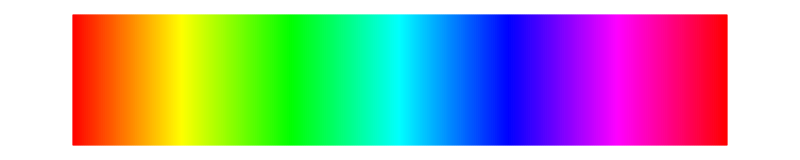

```mathematica
specLine
```

### One Dimensional Interpolation

Here’s a list of numbers:

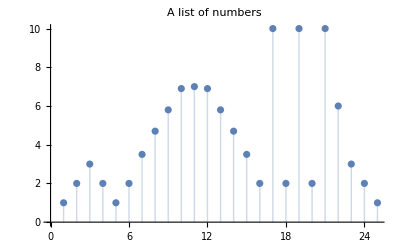

```mathematica
list={1,2,3,2,1,2,3.5,4.7,5.8,6.9,7,6.9,5.8,4.7,3.5,2,10,2,10,2,10,6,3,2,1};
ListPlot[list,Filling->Axis,PlotLabel->"A list of numbers"]
```

What value does this list take on between the elements? None! If we try to find the value that x should have at 4.5, we get an error, as indeed we should.

```mathematica
list[[4.5]]
```

Part::pkspec1: The expression 4.5 cannot be used as a part specification.

{1,2,3,2,1,2,3.5,4.7,5.8,6.9,7,6.9,5.8,4.7,3.5,2,10,2,10,2,10,6,3,2,1}⟦4.5⟧

Yet looking at the plot, it should be pretty clear that if x were to take on a value at 4.5, it should be somewhere between 2 (the value when x=4) and 1 (the value when x=5). We might, for example, split the difference, and say that x[[4.5]] ought to be 1.5. This is a simple form of interpolation called “linear” interpolation (because we are drawing a line between the value at x[[4]] and the value x[[5]]). By making this a function (that passes through all the specified points), it is possible to find out what value the list should have “between the cracks.” As you might imagine, there is not a unique way to do this. The major control is over the “order” of the interpolation.

```mathematica
interpF1 = Interpolation[list, InterpolationOrder -> 1]
```

InterpolatingFunction[{{1., 25.}}, <>]

The output of the interpolation is a function, called the InterpolatingFunction, which we can be used just like any other function. The code above names this output interpF1, and we can find out what values interpF1 has at any given point.

```mathematica
{interpF1[3.5],interpF1[4.5],interpF1[9.3],interpF1[9.5],interpF1[20.1],interpF1[20.9]}
```

{2.5,1.5,6.13,6.35,2.8,9.2}

Observe that interpF1[4.5] is precisely 1.5, just as we had hoped. Here is a plot showing interpF1.

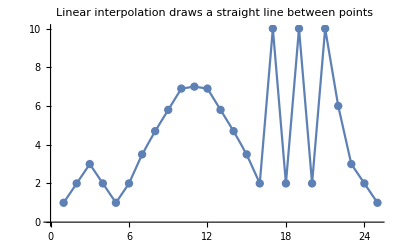

```mathematica
Show[ListPlot[list,PlotStyle->PointSize[0.015],PlotLabel->"Linear interpolation draws a straight line between points"],Plot[interpF1[t],{t,1,25},PlotRange->All]]
```

This linear interpolation draws a straight line between adjacent samples and reports the value of the line at the desired intermediate point. Trying to access interpF1outside of the region over which it was defined gives a warning, though it does use a method (extrapolation) to try and guess what the values might be. Generally it is a good idea to shy away from extrapolation.

```mathematica
{interpF1[-2],interpF1[26],interpF1[29.5]}
```

InterpolatingFunction::dmval: Input value {-2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {26} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {29.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2.,0.,-3.5}

Using other interpolation orders gives slightly different results. The n=0 case adopts the value of the nearest point and is called the “nearest neighbor.” n=2 is called quadratic interpolation.

```mathematica
labelInterpOrd="Different interpolation orders connect the dots more and less smoothly";
infoInterpOrd="Change the interpolation order with the slider.\n\nAt zero, each point defines a flat region.\n\nAt one, the dots are connected with straight lines.\n\nAt higher orders, the dots are connected with higher order polynomials.";
Manipulate[interpF=Interpolation[list,InterpolationOrder->n];
Show[ListPlot[list,PlotStyle->PointSize[0.015]],Plot[interpF[t],{t,1,25},PlotRange->All]],
Row[{Control[{{n,1,"interpolation order"},0,5,1,Appearance->"Labeled"}],Spacer[20],info[infoInterpOrd]}],
FrameLabel->Style[labelInterpOrd,Medium],TrackedSymbols->{n},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Another application of interpolation is to try and find the location of the peak of a signal more accurately. For example, with the default values, the largest value in the sequence below occurs at the 7th location, flanked by smaller values at the 6th and 8th (and then lots of small random values elsewhere). So in a literal sense, the peak occurs at the 7th location. But if the data plausibly comes from samplaing a continuous function, it is likely that the underlying peak of that function occurs somewhat to the left of the 7th peak. Connecting the three points with a quadratic polynimial (i.e., a parabola) provides one way to estimate where the “missing” peak lies: at the top of the parabola! The parabola has three unknown coefficients {a,b,c}, which can be calculated from three points {x1,y1}, {x2,y2}, and {x3,y3} by forming the matrix equation

```mathematica
Row[{MatrixForm[{{x1^2,x1,1},{x2^2,x2,1},{x3^2,x3,1}}],MatrixForm[{a,b,c}],"=",MatrixForm[{y1,y2,y3}] }]
```

(x1^2 | x1 | 1
x2^2 | x2 | 1
x3^2 | x3 | 1)(a
b
c)=(y1
y2
y3)

and multiplying both sides by the matrix inverse.

```mathematica
labelInterpPeak="Interpolation can help to locate peak values";
infoInterpPeak="Change the values of the three central elements with the sliders.\n\nNotice that the peak of the parabola moves smoothly between the nearby points, providing an esimate of the actual location of the peak (which presumably occurs between the sampling instants).";
mInv=Inverse[{{36,6,1},{49,7,1},{64,8,1}}];
Manipulate[Module[{sig,aParab,bParab,cParab,peak,parab,peakVal,title},
sig=Flatten[{RandomVariate[UniformDistribution[{0,0.5}],5],leftVal,centerVal,rightVal,RandomVariate[UniformDistribution[{0,0.5}],5]}];
If[sig[[7]]<sig[[6]],sig[[6]]=sig[[7]]-0.1];
If[sig[[7]]<sig[[8]],sig[[8]]=sig[[7]]-0.01];
{aParab,bParab,cParab}=mInv.{sig[[6]],sig[[7]],sig[[8]]};
parab[x_]:=Clip[aParab x^2+bParab x+cParab,{0,100}];
peak=FindMaximum[parab[z],{z,7}];
peakVal=peak[[2,1,2]];
If[6<peakVal<8,title="Peak value of "~~ToString[peak[[1]]]~~" occurs at "~~ToString[peakVal],title="the middle point needs to be the largest"];
Show[ListPlot[sig,Filling->Axis,PlotRange->All,PlotStyle->PointSize[0.015],PlotLabel->title],Plot[Clip[aParab x^2+bParab x+cParab,{0,100}],{x,5,10},PlotRange->All]]],{{leftVal,3,"left of peak"},0.2,centerVal},{{centerVal,3.2,"central of peak"},1,5},Row[{Control[{{rightVal,1.7,"right of peak"},0.1,centerVal}],Spacer[20],info[infoInterpPeak]}],FrameLabel->Style[labelInterpPeak,Medium],TrackedSymbols->{leftVal,centerVal,rightVal},SaveDefinitions->True]
```

HW: Generate 200 samples of a sine wave of known frequency (specifiable by a slider). Take the discrete Fourier transform of the sine wave and find the largest peak in the spectrum. Using the location of this peak, estimate the frequency. Now implement a paraboic interpolation (as above) to estimate the frequency. Which is more accurate?

HW: Generate 200 samples of a sine wave of known frequency (specifiable by a slider). (a) Take the discrete Fourier transform of the sine wave and find the largest peak in the spectrum. Using the location of this peak, estimate the frequency. (b) Take the discrete Fourier transform of the sine wave, zero-padded with 200 zero-valued samples, find the largest peak in the spectrum. Using the location of this peak, estimate the frequency. (c) Take the discrete Fourier transform of the sine wave, zero-padded with 800 zero-valued samples, find the largest peak in the spectrum. Using the location of this peak, estimate the frequency. (d) Is (a), (b), or (c) more accurate? Can you think of any reason to not continue to pad with 2000, or 20000 zeros?

HW: Compare the answers to the above two HW problems. Explain the advantages and disadvantages of each method.

A good introduction to the way that various kinds of interpolations can be applied to the problem of estimating frequencies can be found in L. Marple, Digital Spectral Analysis: With Applications, Prentice Hall (January 1987).

```mathematica
specLine
```

-Graphics-

### Two Dimensional Interpolation

2D interpolation is pretty much the same as in 1D since it uses the same commands: it just returns a 2D interpolating function. This will need to be plotted in 2D as well, and can be done in any of the ways shown in the representation notebook. Consider a 2D list of values (and the indices of these values) as in list2D, which generates random values in the form needed for the interpolation function, a list of triplets {{index1, index2}, pixel value}.

```mathematica
list2D=Flatten[Table[{{i,j},RandomReal[{0,1}]},{i,1,5},{j,1,5}],1];
Labeled[GraphicsRow[{MatrixForm[Partition[Partition[Flatten[list2D],3][[All,3]],5]],
ListPointPlot3D[Partition[Flatten[list2D],3],ImageSize->300,Filling->Axis,PlotStyle->PointSize[0.04],FillingStyle->Thickness[0.01]]},ImageSize->600],"A two-dimensional list",LabelStyle->captionStyle]
```

-Graphics-A two-dimensional list

As in 1D, the function Interpolation[ ] can be applied to the data to give an interpolating function

```mathematica
interpList2D=Interpolation[list2D,InterpolationOrder->1]
```

InterpolatingFunction[{{1., 5.}, {1., 5.}}, <>]

which can be queried to find values that lie “between the cracks” of the given values.

```mathematica
{interpList2D[2,3],interpList2D[2,3.5],interpList2D[2.5,3],interpList2D[2.5,3.5]}
```

{0.501379,0.569389,0.619349,0.473387}

This can now be plotted as a function over all values in the specified range

```mathematica
Plot3D[interpList2D[x,y],{x,1,5},{y,1,5},PlotLabel->"Linear interpolation in 2D connects points with planar segments"]
```

-Graphics3D-

```mathematica
specLine
```

-Graphics-

As in 1D, the interpolation order describes how smooth the resulting curve is.

```mathematica
labelInterpOrd2D="Different interpolation orders connect the dots more and less smoothly";
infoInterpOrd2D="Change the interpolation order with the chooser box.\n\nAt zero, each point defines a flat region.\n\nAt one, the dots are connected with planes.\n\nAt higher orders, the dots are connected with higher order polynomials.";
Manipulate[interpList2D=Interpolation[list2D,InterpolationOrder->n];
Show[ListPointPlot3D[Partition[Flatten[list2D],3],ImageSize->300,Filling->Axis,PlotStyle->PointSize[0.04]],Plot3D[interpList2D[x,y],{x,1,5},{y,1,5}],ImageSize->400],
Row[{Control[{{n,1,"Interpolation Order"},Range[5]-1,ControlType->SetterBar}],Spacer[20],info[infoInterpOrd2D]}],
FrameLabel->Style[labelInterpOrd2D,Medium],TrackedSymbols->{n},SaveDefinitions->saveDef]
```

Interpolation::innd: First argument in list2D does not contain a list of data and coordinates.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[list2D].

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

ListPointPlot3D::ldata: Flatten[] is not a valid dataset or list of datasets.

Interpolation::innd: First argument in list2D does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPointPlot3D[Flatten[],ImageSize→300,Filling→Axis,PlotStyle→PointSize[0.04]],,ImageSize→400].

```mathematica
specLine
```

-Graphics-

For images, almost all the routines that need to do interpolation handle it transparently. For example, here are two small black and white graphics: a set of concentric rings and a cartoon drawing of a hand and paint brush.

```mathematica
theseImages={Image[Table[0.5 (Sin[4 π E^(-x^2-y^2)]+1.),{x,-1,1,.2},{y,-1,1,.2}]],-Graphics-}
```

{-Graphics-,-Graphics-}

When the size is increased, the individual pixels are clearly visible when using the nearest neighbor method. Applying other interpolation functions produces a smoother visual appearance, though with some blurring of the neighboring values.

```mathematica
labelInterpMeth="Different methods of interpolation give somewhat different results";
infoInterpMeth="Six different methods of interpolation can be easily compared on two images.\n\nNearest neighbor is the simplest; the region surrounding each pixel is colored identically.\n\nBilinear is popular because of its computational simplicity (though it is more complex that Nearest).\n\nOther methods use more complex interpolating functions.\n\nObserve that what looks best for one image may be different from what looks best for another (for example, Lanczos is very smooth for concentric rings, but has jagged edges for the hand & brush).";
Manipulate[ImageResize[Image[theseImages[[i]],ImageSize->All],400,Resampling->meth],
Row[{Control[{{i,1,"image"},{1->"concentric rings",2->"hand & brush"},ControlType->Setter}],Spacer[20],info[infoInterpMeth]}],{{meth,"Nearest","interpolation method"},{"Nearest","Bilinear","Biquadratic","Bicubic","Gaussian","Lanczos"},ControlType->Setter},
FrameLabel->Style[labelInterpMeth,Medium],TrackedSymbols->{i,meth},SaveDefinitions->saveDef]
```

Part::partd: Part specification theseImages⟦1⟧ is longer than depth of object.

Image::imgarray: The specified argument theseImages⟦1⟧ should be an array of rank 2 or 3 with machine-sized numbers.

ImageResize::imginv: Expecting an image or graphics instead of Image[theseImages⟦1⟧,ImageSize→All].

```mathematica
specLine
```

-Graphics-

Whenever any resizing, rotating, or other kind of spatial transformation is happening, there is an interpolation process that occurs. Avoiding the nearest neighbor method will help in removing the blockiness, though each of the other methods has its own kind of subtle artifacts. The next demonstration resizes a small block (55 by 55) block of the x-ray images to 400 by 400 using any of the interpolation methods.

```mathematica
labelInterpMethX="Enlarging a small block with different interpolation methods";
infoInterpMethX="Six different methods of interpolation can be easily compared on segments of x-ray tiles.\n\nNearest neighbor is always the most jagged.\n\nOften there is little difference between the various other methods, though subtle differences are common.";
Manipulate[ImageResize[ImageTake[allImagesXray[[i]],55,55],400,Resampling->meth],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],info[infoInterpMethX]}],{{meth,"Nearest","interpolation method"},{"Nearest","Bilinear","Biquadratic","Bicubic","Gaussian","Lanczos"},ControlType->Setter},
FrameLabel->Style[labelInterpMethX,Medium],TrackedSymbols->{i,meth},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Similar changes occur when doing the interpolation on the red, green, and blue channels separately.

```mathematica
labelInterpMethC="Similar effects occur when interpolating in color";
infoInterpMethC="Six different methods of interpolation can be easily compared on segments of various color.\n\nNearest neighbor is always the most jagged.\n\nOften there is little difference between the various other methods, though subtle differences are common.";
Manipulate[ImageResize[ImageTake[allImagesColor[[i]],{300,355},{300,355}],400,Resampling->meth],Row[{Control[{{i,vanSheep,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoInterpMethC]}],{{meth,"Nearest","interpolation method"},{"Nearest","Bilinear","Biquadratic","Bicubic","Gaussian","Lanczos"},ControlType->Setter},
FrameLabel->Style[labelInterpMethC,Medium],TrackedSymbols->{i,meth},SaveDefinitions->saveDef]
```

Part::partd: Part specification allImagesColor⟦6⟧ is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of allImagesColor⟦6⟧.

ImageResize::imginv: Expecting an image or graphics instead of ImageTake[allImagesColor⟦6⟧,{300,355},{300,355}].

```mathematica
specLine
```

-Graphics-

### How Bilinear Interpolation Works: A Case Study

Suppose the values of the pixels are known at the four corners of a box and the goal is to estimate the value at some intermediate point within the box. In symbols, suppose that g[x1,y1], g[x2,y1], g[x1,y2] and g[x2,y2] are known. Assuming x’ lies between x1 and x2 and that y’ lies between y1 and y2, bilinear interpolation estimates g[x’, y’] using the equation

```mathematica
g[x_,y_]:=a x+b y+ c x y + d
```

For example, if the pixel values at the four corners are 5, 10, 5, and 20 as shown in the figure below

```mathematica
Labeled[Row[{Image[-Graphics-,ImageSize->200],Spacer[50],Image[-Graphics-,ImageSize->200]}],"The values of the pixels at the four corners are known, what should the value at the red dot be?",LabelStyle->captionStyle]
```

-Graphics--Graphics-The values of the pixels at the four corners are known, what should the value at the red dot be?

This can be written algebraically as the four equations

```mathematica
{g[3,5], g[4,5], g[3,6],g[4,6]}
```

{3 a+5 b+15 c+d,4 a+5 b+20 c+d,3 a+6 b+18 c+d,4 a+6 b+24 c+d}

which represent a collection of 4 equations in four unknowns (a,b,c,d). Hence they can be solved for the unknowns:

```mathematica
Solve[{5,10,5,20}=={g[3,5],g[4,5],g[3,6],g[4,6]},{a,b,c,d}]
```

{{a→-45,b→-30,c→10,d→140}}

Now that the a,b,c,d parameters are known, it’s easy to plug in any point, such as {x’,y’}={3.8, 5.8} to find that the appropriate value

```mathematica
a x+b y+c x y+d//.{{a->-45,b->-30,c->10,d->140,x->3.8,y->5.8}}
```

{15.4}

as shown in the figure above. Alternatively, the four equations and four unknown can be gathered into matrix form

```mathematica
m[x1_,y1_,x2_,y2_]:={{x1,y1,x1 y1,1},{x2,y1,x2 y1,1},{x1,y2,x1 y2,1},{x2,y2,x2 y2,1}};
gVec={"g[x1,y1]","g[x2,y1]","g[x1,y2]","g[x2,y2]"};
Row[{MatrixForm[m[x1,y1,x2,y2]],MatrixForm[{a,b,c,d}],"=",MatrixForm[gVec]}]
```

(x1 | y1 | x1 y1 | 1
x2 | y1 | x2 y1 | 1
x1 | y2 | x1 y2 | 1
x2 | y2 | x2 y2 | 1)(a
b
c
d)=(g[x1,y1]
g[x2,y1]
g[x1,y2]
g[x2,y2])

and then solved by multiplying both sides of the equation by m inverse (or, numerically preferable, by using a least squares method).

```mathematica
Inverse[m[3,5,4,6]].{5,10,5,20}
```

{-45,-30,10,140}

Using the solution to this linear system, the appropriate value at the interior point {x’,y’}={3.8, 5.8} is again

```mathematica
a x+b y+c x y+d//.{{a->-45,b->-30,c->10,d->140,x->3.8,y->5.8}}
```

{15.4}

which is the interpolated value at the red dot located at {x’,y’}={3.8,5.8}. All other points within the green box use the same set of {a,b,c,d} values. Here, for the sake of verification, is the same problem solved using the built in interpolation function. The list box2D sets up the four corners of the box and interpBox creates the interpolating function (in this case, identical to the linear map above). Of course, the answer at the point {3.8,5.8} is the same as before.

```mathematica
box2D={{{3,5},5},{{4,5},10},{{3,6},5},{{4,6},20}};
interpBox=Interpolation[box2D,InterpolationOrder->1];
interpBox[3.8,5.8]
```

15.4

HW: Create a demonstration that builds a 2D parabolic surface to try and find the location of the peak of a 2D signal more accurately. Mimic the construction in the 1D case.